Thomas Kwok
Math 385

# Homework 4

## Problem 1

For n = 50 states, use the power method with a tolerance of 10^-5 and up to 100 iterations, to estimate the spectral radius of the iteration matrix I - BA. Let your initial eigenvector be (1; 1; 1; ... ; 1) and use difference between successive eigenvalues |lk - lk-1| to check your tolerance.

a. Do this for B = D^-1 where D is the diagonal matrix formed from the diagonal entries of the coefficient matrix A.

```mathematica
n = 50;
A = Table[If[i== j, 1, If[Abs[i-j] == 1, -1/2, 0]], {i, 50}, {j, 50}];
diag = Table[If[i== j, 1, If[Abs[i-j] == 0, -1/2, 0]], {i, n}, {j, n}];
table = {};
b = Inverse[diag];
itermat = IdentityMatrix[n] - (b.A);
iter = 1;
tol = 1;
x0 = Table[1., n];
While[tol > 10^-5 && iter ≤ 100,
xnew = (itermat.x0/Norm[itermat.x0]);
tol = Abs[(Norm[A.xnew]/Norm[xnew])-(Norm[A.x0]/Norm[x0])];
AppendTo[table, {iter, tol, xnew, x0}];
x0 = xnew;
iter++];
jacobi = PrependTo[table, {"iteration", "|lk-lk-1|"}];
Grid[jacobi, Dividers-> All];
specradius = Norm[itermat.x0]/Norm[x0]
```

0.998025

b. Repeat part (a) for B = (L + D)^-1 where L is the strictly lower triangular entries of the coefficient matrix A.

```mathematica
n = 50;
A = Table[If[i== j, 1, If[Abs[i-j] == 1, -1/2, 0]], {i, 50}, {j, 50}];
lower = LowerTriangularize[A];
diag = Table[If[i== j, 1, If[Abs[i-j] == 0, -1/2, 0]], {i, n}, {j, n}];
diag2 = diag+lower;
table = {};
b = Inverse[diag2];
itermat2 = IdentityMatrix[n] - (b.A);
iter = 1;
tol = 1;
x0 = Table[1., n];
While[tol > 10^-5 && iter ≤ 100,
xnew = (itermat2.x0/Norm[itermat2.x0]);
tol = Abs[(Norm[A.xnew]/Norm[xnew])-(Norm[A.x0]/Norm[x0])];
AppendTo[table, {iter, tol}];
x0 = xnew;
iter++];
dataheading = PrependTo[table, {"iteration", "|lk-lk-1|"}];
gauss = Grid[dataheading, Dividers-> All];
specradius2 = Norm[itermat2.x0]/Norm[x0]
```

0.998589

c. Compare your calculated values with the true spectral radius computed using Mathematica’s Eigenvalues function.

```mathematica
A = Table[If[i== j, 1, If[Abs[i-j] == 1, -1/2, 0]], {i, 50}, {j, 50}];
tablec= {Max[Abs[Eigenvalues[N[itermat]]]], Max[Abs[Eigenvalues[N[itermat2]]]], specradius, specradius2};
Grid[PrependTo[Table[tablec, {i, 1}], {"true B=D^-1", "true B=(L+D)^-1", "B=D^-1 Spectral Radius", "B=(L+D)^-1 Spectral Radius"}], Dividers->All]
```

Set::write: Tag Table in Table[tablec,{i,1}] is Protected.

true B=D^-1 | true B=(L+D)^-1 | B=D^-1 Spectral Radius | B=(L+D)^-1 Spectral Radius
0.998103 | 0.998736 | 0.998025 | 0.998589

d. Comment on the convergence of the Jacobi and Gauss-Seidel methods for solving the linear system.

Theoretically, the rate of convergence for the Gauss-Seidel method is faster than the Jacobi method. The difference between the two is that for Jacobi, we take B= D^-1 while for Gauss-Seidel we take B=(L+D)^-1. In the Jacobi method, the xi^k value does not change until the (k+1) iteration is run. The Gauss-Seidel is more efficient and thus converges faster because it uses the xi^k value as soon as it is known, so it does not need to wait until the (k+1) iteration.

## Problem 2

Implement the Jacobi method to solve the linear system with the stop tolerance of 10^-2 .Use the normed error between successive estimates to check the tolerance. Display a line plot of the error against the iteration number.

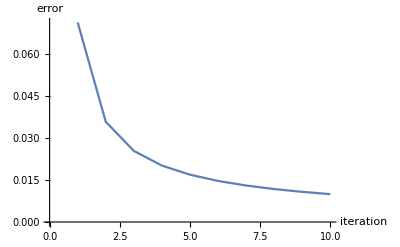

```mathematica
n = 50;
A = Table[If[i== j, 1, If[Abs[i-j] == 1, -1/2, 0]], {i, n}, {j, n}];
b= Table[If[i==1, 1/2, 0], {i, n}];
diag = Table[If[i== j, 1, If[Abs[i-j] == 0, -1/2, 0]], {i, n}, {j, n}];
inversediag = Inverse[diag];
ident = IdentityMatrix[n];
table = {};
tol = 1;
x0 = Table[1, n];
k = 1;
summ=Table[0, n];
While[tol > 10^-2 && k ≤ 100,
xnew = (ident-inversediag.A).x0 + inversediag.b;
tol = Abs[(Norm[xnew-x0])/Norm[xnew]];
AppendTo[table, {k, tol}];
k++;
x0 = xnew;]
ListLinePlot[table, AxesLabel-> {"iteration", "error"}]
```

## Problem 3

Implement the Gauss-Seidel method to solve the linear system. Compare the number of iterations with the Jacobi method. Comment on your results. Display a line plot of the error against the iteration number.

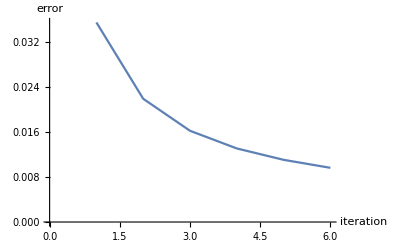

```mathematica
n = 50;
A = Table[If[i== j, 1, If[Abs[i-j] == 1, -1/2, 0]], {i, n}, {j, n}];
b= Table[If[i==1, 1/2, 0], {i, n}];
diag = Table[If[i== j, 1, If[Abs[i-j] == 0, -1/2, 0]], {i, n}, {j, n}];
l = LowerTriangularize[A];
u = UpperTriangularize[A];
inversediag = Inverse[diag+l];
ident = IdentityMatrix[n];
table = {};
tol = 1;
x0 = Table[1, n];
k = 1;
While[tol > 10^-2 && k ≤ 100,
xnew = (ident-inversediag.A).x0 + inversediag.b;
tol = Abs[(Norm[xnew-x0])/Norm[xnew]];
AppendTo[table, {k, tol}];
x0 = xnew;
k++;]
ListLinePlot[table, AxesLabel-> {"iteration", "error"}]
```

## Problem 4

Set n = 100, 1000, 5000, 10,000. Apply Gauss seidel method to solve the linear system and calculate cpu time. Plot the cpu time versus the size of the matrix and comment on result. Compare to Problem 5 in HW 3 and comment on your result.

```mathematica
n = 100;
A = Table[If[i== j, 1, If[Abs[i-j] == 1, -1/2, 0]], {i, n}, {j, n}];
b= Table[If[i==1, 1/2, 0], {i, n}];
diag = Table[If[i== j, 1, If[Abs[i-j] == 0, -1/2, 0]], {i, n}, {j, n}];
l = LowerTriangularize[A];
u = UpperTriangularize[A];
inversediag = Inverse[diag+l];
ident = IdentityMatrix[n];
tol = 1;
x0 = Table[1, n];
k = 1;
Timing[While[tol > 10^-2 && k ≤ 100,
xnew = (ident-inversediag.A).x0 + inversediag.b;
tol = Abs[(Norm[xnew-x0])/Norm[xnew]];
AppendTo[table, {k, tol}];
x0 = xnew;
k++;]]
```

{0.046875,Null}

```mathematica
n = 1000;
A = Table[If[i== j, 1, If[Abs[i-j] == 1, -1/2, 0]], {i, n}, {j, n}];
b= Table[If[i==1, 1/2, 0], {i, n}];
diag = Table[If[i== j, 1, If[Abs[i-j] == 0, -1/2, 0]], {i, n}, {j, n}];
l = LowerTriangularize[A];
u = UpperTriangularize[A];
inversediag = Inverse[diag+l];
ident = IdentityMatrix[n];
tol = 1;
x0 = Table[1, n];
k = 1;
Timing[While[tol > 10^-2 && k ≤ 100,
xnew = (ident-inversediag.A).x0 + inversediag.b;
tol = Abs[(Norm[xnew-x0])/Norm[xnew]];
AppendTo[table, {k, tol}];
x0 = xnew;
k++;]]
```

{1.79688,Null}

```mathematica
table1 = {{100, .046875}, {1000, 1.79688}};
table2 = {{100, .03125}, {1000, 1.54688}};
ListLinePlot[{table1,table2}, AxesLabel-> {"Matrix Size", "CPU Time"}, PlotLabels->{"Homework 4 CPU Data", "Homework 3 CPU Data"}]
```

-Graphics-

My data is not supportive of the purpose of the Gauss-Seidel iteration method. The method is supposed to have a faster solver time than a simple linear solve but my data does not support this. In addition, the Gauss-Seidel crashed my computer for 5000 and 10,000 consistently, which lets me know that the difference between the homework data increases drastically the large the matrix size is. The reason for this is because the code I am using is running the matrix multiplication for each iteration, which utilizes too much CPU space and thus crashes my system. Also it seemed that since I have defined several matrices using n, the code is having a tough time creating the matrix for when n=5000, as running that code with no iteration in itself already crashes my computer.

## Problem 5

Consider the function f(x,y) = x^2 + xy + y^2.

1. Perform one iteration of gradient descent by hand to estimate the minimum of f(x,y) using the initial seed (2,1).
2. Using the same seed, perform one iteration of the Hessian method by hand to estimate a minimum for f(x,y).
3. Comment on result

-Graphics-		

The Hessian and Gradient test tells me that there is a local maxima at <.31967, -.34426>  for f(x,y) = x^2 + xy + y^2 as the determinant is greater than 0 and the first term is also greater than 0.

## Problem 6

```mathematica
mata = {{4, -2, 3, -5}, {3, 3, 5, -8}, {-6, -1, 4, 3}, {-4, 2, -3, 5}};
p0 = {5, 5, 5, 5};
b = {1, 1, 1, -1};
f[x_,y_, z_, w_] = {{4x-2y+3z-5w}, {3x+3y+5z-8w}, {-6x-y+4z+3w}, {-4x+2y-3z+5w}};
grad[x_,y_, z_, w_]={D[f[x,y,z,w],x],D[f[x,y,z,w],y], D[f[x,y,z,w],z], D[f[x,y,z,w],w]};
maxitr = 35;
i=1;
tol = 1;
While[i≤ maxitr && tol > 10^-5;
gradvec = gradf[p0[[1]],p0[[2]], p0[[3]], p0[[4]]];
searchd = -gradvec/Sqrt[gradvec.gradvec];
stepfun[t_]=f[p0[[1]]+t*searchd[[1]],p0[[2]]+t*searchd[[2]], p0[[2]]+t*searchd[[3]], p0[[2]]+t*searchd[[4]]];
stepLength[stepfun,0,35];
p1=p0+hmin*searchd;
If[f[p1[[1]],p1[[2]], p1[[3]], p1[[4]]]<f[p0[[1]],p0[[2]], p0[[3]], p0[[4]]],
Print["Iteration ", i, " was successful"];
p0=p1,
tol = f[p1[[1]],p1[[2]], p1[[3]], p1[[4]]];
Print["Iteration ",i," failed to reduce function"]];
Print[p0]]
```

{{-5 w+4 x-2 y+3 z},{-8 w+3 x+3 y+5 z},{3 w-6 x-y+4 z},{5 w-4 x+2 y-3 z}}

Part::partw: Part 4 of -gradf[5,5,5,5]/(√(gradf[5,5,5,5].gradf[5,5,5,5])) does not exist.

{5,5,5,5}

b. Use Linear Solve and compare your results

```mathematica
mata = {{4, -2, 3, -5}, {3, 3, 5, -8}, {-6, -1, 4, 3}, {-4, 2, -3, 5}};
b = {1, 1, 1, -1};
LinearSolve[mata, b]
```

{3/197,-19/197,49/197,0}

Since this equation uses the function Linear Solve, it only gives one solution, which isn’t necessarily the best solution or the absolute minimum of the equation. Technically the answer for 6a should be a stronger solution than this, but I was unable to get a solution to 6a.